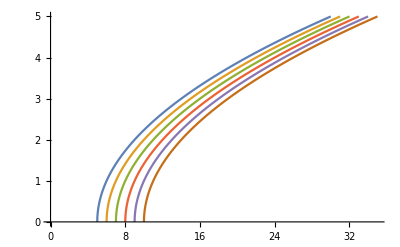

```mathematica
Module[{h,PH},
h[t_,p_]=t+p^2;
PH=Table[{h[T,P],P},{T,5,10},{P,0,5,0.1}];
ListPlot[PH,Joined->True]
]
```

```mathematica
Manipulate[
Module[{h,g,PH01,PH02,PH1,PH2,PH3,p1,p2,p3},
h=T+P^2;
g[z_]=z*1;

PH01=Table[{h,P},{P,0,5,0.1}];
PH02=Quiet@Interpolation[PH01];
PH1=Table[PH01,{T,5,10}];
PH2=Table[PH02,{T,1,5}];
PH3=Interpolation[PH2];

p1=ListPlot[PH1,Joined->True];
p2=ListPlot[PH2,Joined->True];
(*p3=Plot[PH3[x],{x,1,5}];*)
p3=Graphics[{Text[g[PH1]]},PlotRange->All,ImageSize->Full];
(*p2=Graphics[Text@"poo"];*)

Show[Switch[cs,1,p1,2,p2,3,p3]]
],
Control[{{cs,3,""},{1->" p1 ",2->" p2 ",3->" p3 "},Setter}]
]
```